# Signal Processing - Project 2

## William Lewin & Elias Chahine wlewin@kth.se echahine@kth.se

## Part 1

### Assignment

Introduce the system function of an IIR-filter as
H(z)=((1-z^-1)  ∏_(k=1)^4 (1-z^-1 e^(-i (2k-1)(11π)/100))(1-z^-1 e^(i (2k-1)(11π)/100)))/(100 ∏_(k=1)^4 (1-0.9 z^-1 e^(-i k(11π)/50))(1-0.9 z^-1 e^(i k(11π)/50)))

Make a pole-zero plot of H(z). Is the system stable?

Discuss how the filter works, what happens with certain frequencies?

Illustrate the frequency response of the IIR.

Sketch a direct form structure to illustrate the IIR.

Introduce the signal x(t)=1/π∑_(k=1)^9 (-1)^(k-1)/k sin(2 π f_0 k t), f_0=220Hz. This signal is sampled with the frequency f_s=4kHz. Plot the sampled signal x[n].

Now, the signal x[n] is input to the IIR above. Compute and plot the output signal y[n].

Finally, draw and compare the two-sided spectrum of x[n] and y[n].

### Discussion

### Code

```mathematica
ClearAll[".b4*"]
```

#### Package II1303

```mathematica
(* Ver. 151125, goeran@kth.se *)
BeginPackage["II1303`"]; 
Unprotect[{ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 
Reconstruct::usage = "Reconstruct[fs][{f,A,ϕ}] returns the shifted or folded  \
{f,A,ϕ} list due to sampling. Reconstruct[ωs][{ω,A,ϕ}] is also valid.";
fAϕ::usage = "fAϕ[t][Cos|Sin|Exp[arg]] extracts {f,A,ϕ} information.";
ωAϕ::usage = "ωAϕ[t][Cos|Sin|Exp[arg]] extracts {ω,A,ϕ} information.";
ToExp::usage = "ToExp[z] = Abs[z]*E^(I*Arg[z]) returns a complex number in \
exponential form.\nFor floating point complex numbers use ReleaseHold in orer to \
evaluate."; 
TrigCombine::usage = "ToExp[a*trig[x+α] + b*trig[x+β]], where trig is Cos or Sin, \
returns A*trig[x+v].";
Poles::usage = "Poles[H, z] returns the poles of the system function H[z]."; 
Zeros::usage = "Zeros[H, z] returns the zeros of the system function H[z]."; 
PoleZeroPlot::usage = "PoleZeroPlot[H, z] plots poles and zeros of the system \
function H[z].\nPoleZeroPlot takes the same options as ListPlot."; 
PoleMarker::usage = "PoleMarker is an option for PoleZeroPlot that defines the \
graphics for the pole marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...]."; 
ZeroMarker::usage = "ZeroMarker is an option for PoleZeroPlot that defines the \
graphics for the zero marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...].";
MarkerScale::usage = "MarkerScale is an option for PoleZeroPlot that defines the \
scale for the pole and zero marker."; 
ZTransform2::usage = "ZTransform2[x, n, z] returns the bilateral, 1D z-transform.\n\
It evaluates FourierSequenceTransform[x,n,-I Log[z]]."; 
InverseZTransform2::usage = "InverseZTransform2[X, z, n] returns the bilateral, 1D \
inverse z-transform.\nIt evaluates InverseFourierSequenceTransform[X /. z -> \
E^(I*ω), ω, n]."; 
FactorAll::usage = "FactorAll[p, x] returns a product of first degree factors."; 
ZApart::usage = "ZApart[X, z] = Expand[z*Apart[X/z,z]] returns an expression \
suitable for inverse z-transform."; 
LaplaceTransform2::usage = "LaplaceTransform2[x, t, s] returns the bilateral, 1D \
Laplace transform.\nIt evaluates FourierTransform[x, t, -I*s]."; 
InverseLaplaceTransform2::usage = "InverseLaplaceTransform2[X, s, t] returns the \
bilateral, 1D inverse Laplace transform.\nIt evaluates InverseFourierTransform[X /. \
s -> I*ω, ω, t].";
 
Begin["`Private`"];
Reconstruct[(fs_)?Positive][{f_,A_,ϕ_}]:=
Module[
	{fa,ϕa=ϕ},
	(* shift *)
	fa=Mod[Abs[f], fs];
	(* fold *)
	If[fa>fs/2,fa=fs-fa;ϕa=-ϕ];
	If[fa>0,{Sign[f]*fa,A,ϕa},{0,A,ϕa}]
];

Reconstruct[fs_][data:{{_, _, _}..}] := 
Module[{data1,data2,data3}, 
	data1 = Reconstruct[fs] /@ data;
	data2 = Gather[data1, #1[[1]] == #2[[1]] & ];
	({#1[[1,1]], Norm[#1[[All,2]] . E^(I*#1[[All,3]])], Arg[#1[[All,2]] . E^(I*#1[[All,3]])]} & ) /@ data2
];

fAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]+Arg[A]};
fAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
fAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/(2π ⅈ),Abs[A],Coefficient[z,t,0]/ⅈ+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/ⅈ,Abs[A],Coefficient[x,t,0]/ⅈ+Arg[A]};
 
ToExp[z:Complex[_Real, _Real]] := Abs[z]*HoldForm[E]^(I*Arg[z]); 
ToExp[(z_)?NumericQ] := Abs[z]*E^(I*Arg[z]); 
ToExp[z___] := z; 
SetAttributes[ToExp, Listable];

TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Cos[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) + b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) - I*b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Sin[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[(-I)*a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
SetAttributes[TrigCombine, HoldAll];

Poles[H_, z_Symbol] := Flatten[
	TransferFunctionPoles[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Poles[H:_Symbol | _Function, z_Symbol] := Poles[H[z], z];
 
Zeros[H_, z_Symbol] := Flatten[
TransferFunctionZeros[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Zeros[H:_Symbol | _Function, z_Symbol] := Zeros[H[z], z];
 
Options[PoleZeroPlot] = Join[{
	PoleMarker :> ({
		Red, 
		Line[{#1 + #3*{-1, -1}/√2, #1 + #3*{1, 1}/√2}], 
		Line[{#1 + #3*{-1, 1}/√2, #1 + #3*{1, -1}/√2}], 
		If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ), 
	ZeroMarker :> ({
		Blue, 
		Circle[#1, #3], 
        If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ),
	MarkerScale -> Automatic
	}, 
	Options[Graphics]
]; 
SetOptions[PoleZeroPlot, AspectRatio -> Automatic, Axes -> True, PlotRange -> Automatic]; 
PoleZeroPlot[H_, z_Symbol, opts:OptionsPattern[]] := Module[
	{xy, x, y, d, pp, pz, mp, mz, s, r, 𝕡, 𝕫, range, allopts, s0=Scaled[0.015]}, 
	xy := {Re[#1], Im[#1]} & ; 𝕡 = Poles[N[H], z]; 𝕫 = Zeros[N[H], z]; 
	pp = xy /@ DeleteDuplicates[𝕡]; pz = xy /@ DeleteDuplicates[𝕫]; 
	mp = Length /@ Gather[𝕡]; mz = Length /@ Gather[𝕫]; 
	x = Join[pz[[All,1]], pp[[All,1]]]; y = Join[pz[[All,2]], pp[[All,2]]]; 
	If[OptionValue[PlotRange] === Automatic, 
		x = Join[{-1, 1}, x]; y = Join[{-1, 1}, y]
	]; 
	range = ({Min[#1], Max[#1]} & ) /@ {x, y}; 
	d = 0.05*Apply[Subtract, range, {1}]; range = range + Transpose[{d, -d}]; 
	allopts = FilterRules[Join[{opts}, Options[PoleZeroPlot]], Options[Graphics]]; 
	If[OptionValue[PlotRange] === Automatic || OptionValue[PlotRange] === All, 
		PrependTo[allopts, PlotRange -> range]
	]; 
	s = OptionValue[MarkerScale];
	If[ s=== Automatic, s = s0];
	If[ ! MatchQ[s, _?NumericQ] && ! MatchQ[s, Scaled[_?NumericQ]], s = s0];
	If[MatchQ[s, Scaled[_?NumericQ]],
		s = First[s];
		r = PlotRange/.AbsoluteOptions[Graphics[Point[Join[pp,pz]],Sequence @@ allopts],PlotRange];
		If[MatchQ[r,{{_?NumberQ,_?NumberQ},{_?NumberQ,_?NumberQ}}],s*=Min[-Subtract@@@r]]
	];
	Graphics[{
		Apply[OptionValue[PoleMarker], (Join[#1, {s}] & ) /@ Transpose[{pp, mp}], {1}], 
		Apply[OptionValue[ZeroMarker], (Join[#1, {s}] & ) /@ Transpose[{pz, mz}], {1}]
		}, Sequence @@ allopts
	]
];
PoleZeroPlot[H:_Symbol | _Function, z_Symbol, opts:OptionsPattern[]] := PoleZeroPlot[H[z], z, opts]; 

Options[ZTransform2] = Rest[Options[FourierSequenceTransform]]; 
ZTransform2[x_, n_Symbol, z_, opts:OptionsPattern[]] := 
	FourierSequenceTransform[x, n, (-I)*Log[z], FourierParameters -> {1, 1}, opts];
ZTransform2[x:_Symbol | _Function, n_Symbol, z_, opts:OptionsPattern[]] := 
	ZTransform2[x[n], n, z, opts]; 

Options[InverseZTransform2] = Rest[Options[InverseFourierSequenceTransform]]; 
InverseZTransform2[X_, z_Symbol, n_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierSequenceTransform[X /. z -> E^(I*ω), ω, n, FourierParameters -> {1, 1}, opts]
]; 
InverseZTransform2[X:_Symbol | _Function, z_Symbol, n_, opts:OptionsPattern[]] := 
	InverseZTransform2[X[z], z, n, opts];

FactorAll[p_, x_Symbol] := Module[
{a, z, q}
, a = Coefficient[p, x, Exponent[p, x]]; 
q = p/a; z = x /. Solve[q == 0, x, Complexes]; 
Times @@ Join[{a}, x - z]
] /; PolynomialQ[p, x];

ZApart[X_, z_Symbol] := Expand[z*Apart[X/z, z]];
 
Options[LaplaceTransform2] = Most[Options[FourierSequenceTransform]]; 
LaplaceTransform2[x_, t_Symbol, s_, opts:OptionsPattern[]] := 
	FourierTransform[x, t, (-I)*s, FourierParameters -> {1, -1}, opts];
LaplaceTransform2[x:_Symbol | _Function, t_Symbol, s_, opts:OptionsPattern[]] := 
	LaplaceTransform2[x[t], t, s, opts]; 

Options[InverseLaplaceTransform2] = Most[Options[InverseFourierSequenceTransform]]; 
InverseLaplaceTransform2[X_, s_Symbol, t_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierTransform[X /. s -> I*ω, ω, t, FourierParameters -> {1, -1}, opts]
]; 
InverseLaplaceTransform2[X:_Symbol | _Function, s_Symbol, t_, opts:OptionsPattern[]] := 
	InverseLaplaceTransform2[X[s], s, t, opts];
 
End[];
 
Protect[{Reconstruct, fAϕ, ωAϕ, ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 

EndPackage[];
```

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_?Positive][{f_,A_,ϕ_}] is Protected.

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_][data:{{_,_,_}..}] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

#### The rest

```mathematica
H[z_]:=((1-z^-1)∏_(k=1)^4 ((1-z^-1 ⅇ^(-ⅉ (2k-1)(11 π)/100)) (1-z^-1 ⅇ^(ⅉ (2k-1)(11 π)/100))))/(100∏_(k=1)^4 ((1-0.9 z^-1 ⅇ^(-ⅉ k(11 π)/50)) (1-0.9 z^-1 ⅇ^(ⅉ k(11 π)/50))))
```

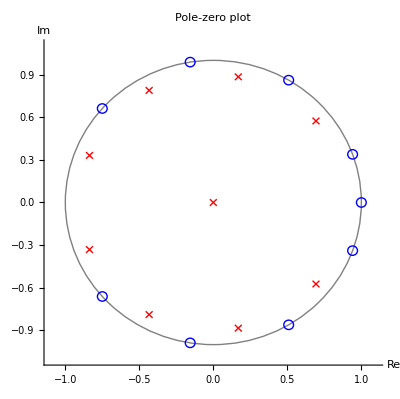

```mathematica
PoleZeroPlot[H[z],z,AxesLabel->{"Re","Im"},Prolog ->{Gray, Circle[]},PlotLabel->"Pole-zero plot"]
```

```mathematica
(*The system is stable. All the poles are located within the unit circle; meaning that the response signal will weaken with time and not grow to infinity *)
```

```mathematica
(*The filter works as a high-pass filter of sorts. Some frequencies are removed completely. *)
```

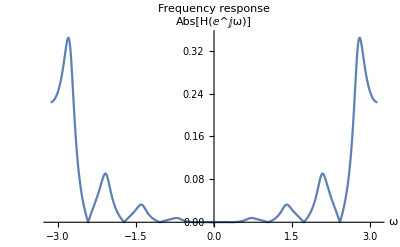

```mathematica
Plot[Abs[H[ⅇ^(ⅉ*ω)]], {ω, -π, π},PlotRange->{{-Pi,Pi},{0,0.35}}, AxesLabel->{"ω", HoldForm[Abs[H[ⅇ^ⅉω]]]},PlotLabel->"Frequency response"]
```

## Part 2

### Assignment

Introduce the following signal

x(t)=(ⅇ^(-50 t) cos(2 π 100 t)+ⅇ^(-75 t) cos(2 π 200 t)+ⅇ^(-100 t) cos(2 π 300 t))u(t)

Make a plot of x(t).

Compute the spectrum X(j ω).

Plot Abs[X(j ω)] and arg(X(j ω)).

There are some distinct local maxima and minima in the spectrum. Solve for these frequencies.

Can you motivate the local maxima from the expression x(t)?

### Discussion

### Code